```mathematica
ρ=Sphere[{0,0,0},10] (*Can use Ball[] instead of Sphere[] if we want points inside the Sphere*)
```

Sphere[{0,0,0},10]

```mathematica
Graphics3D[ρ]
```

-Graphics3D-

```mathematica
γ=RandomPoint[ρ,2500]
```

{{-3.44757,1.93433,9.18546},{5.22089,-5.8771,6.18078},{-0.0494672,7.58006,6.52229},{-3.63679,-3.75575,8.52456},{-6.2312,2.9712,-7.23493},2491,{-4.70449,-8.23397,-3.17325},{-6.63345,-5.42089,5.15861},{-8.85346,-3.80494,2.67184},{-9.06219,3.91578,1.59479}}
 |  |  |  |

```mathematica
Graphics3D[Point[γ], Boxed->False]
```

-Graphics3D-

## alpha shape

```mathematica
circumRadius=Compile[{{v,_Real,2}},With[{a=v[[1]]-v[[4]],b=v[[2]]-v[[4]],c=v[[3]]-v[[4]]},With[{a1=Plus@@(a^2),b1=Plus@@(b^2),c1=Plus@@(c^2),α1=b[[2]] c[[3]]-b[[3]] c[[2]],α2=b[[3]] c[[1]]-b[[1]] c[[3]],α3=b[[1]] c[[2]]-b[[2]] c[[1]],β1=c[[2]] a[[3]]-c[[3]] a[[2]],β2=c[[3]] a[[1]]-c[[1]] a[[3]],β3=c[[1]] a[[2]]-c[[2]] a[[1]],γ1=a[[2]] b[[3]]-a[[3]] b[[2]],γ2=a[[3]] b[[1]]-a[[1]] b[[3]],γ3=a[[1]] b[[2]]-a[[2]] b[[1]]},Norm[a1 {α1,α2,α3}+b1 {β1,β2,β3}+c1 {γ1,γ2,γ3}]/(2 Norm[Plus@@(a[[1;;3]] {α1,α2,α3})])]],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CompiledFunction[…]

```mathematica
alphaShapes[points_,crit_]:=Module[{alphacriteria,del=Quiet@DelaunayMesh@points,tetras,tetcoords,tetradii,selectExternalFaces},alphacriteria[tetrahedra_,radii_,rmax_]:=Pick[tetrahedra,UnitStep@Subtract[rmax,radii],1];
selectExternalFaces[facets_]:=MeshRegion[points,facets];
If[Head[del]===EmptyRegion,del,tetras=MeshCells[del,3];
tetcoords=MeshPrimitives[del,3][[All,1]];
tetradii=Quiet@circumRadius@tetcoords/.ComplexInfinity->$MaxMachineNumber;
selectExternalFaces@alphacriteria[tetras,tetradii,crit]]]
```

```mathematica
region[α_]:=RegionBoundary@alphaShapes[data,α]
```

```mathematica
data=γ
```

{{-3.44757,1.93433,9.18546},{5.22089,-5.8771,6.18078},{-0.0494672,7.58006,6.52229},{-3.63679,-3.75575,8.52456},{-6.2312,2.9712,-7.23493},2491,{-4.70449,-8.23397,-3.17325},{-6.63345,-5.42089,5.15861},{-8.85346,-3.80494,2.67184},{-9.06219,3.91578,1.59479}}
 |  |  |  |

```mathematica
Manipulate[region[a],{a,0,20}]
```

```mathematica
λ=region[30]
```

-Graphics3D-

## curvature

```mathematica
mps2=MeshPrimitives[λ,2];
coords=First/@mps2;
```

```mathematica
nbhCurv[neighborhood_]:=Module[{N=neighborhood},
𝒲=MeshRegion[Flatten[N,1],Triangle/@Partition[Table[i1,{i1,1,Length@Flatten[N,1]}],3]];
l=Table[Length[Extract[N,Partition[First/@Position[N,MeshPrimitives[𝒲,0][[i1,1]]],1]]],{i1,1,Length@MeshCells[𝒲,0]}];
centerIndex=(Flatten@Position[l,Max[l]])[[1]];
K[neighb_,region_,index_,ctrIndex_]:=Module[{myNBH=neighb,𝒲K=region,idx=index,centerIndex0=ctrIndex,i,j},{i,j}={Extract[myNBH,Partition[First/@Position[myNBH,MeshPrimitives[𝒲,0][[idx,1]]],1]][[1]],Extract[myNBH,Partition[First/@Position[myNBH,MeshPrimitives[𝒲K,0][[idx,1]]],1]][[2]]};
outerPoint=MeshPrimitives[𝒲K,0][[idx,1]];
thirdPointi=Flatten@i[[Flatten@Position[Table[!MemberQ[{Flatten[Position[i,center],1],Flatten@(Position[i,outerPoint])},{k}],{k,3}],True]]];
(*sharedLine=Line[{MeshPrimitives[𝒲,0][[centerIndex0,1]],outerPoint}];*)
center=MeshPrimitives[𝒲K,0][[centerIndex0,1]];
thirdPointj=Flatten@j[[Flatten@Position[Table[!MemberQ[{Flatten[Position[j,center],1],Flatten@(Position[j,outerPoint])},{k}],{k,3}],True]]];
edgeVec1i=thirdPointi-center;
edgeVec2i=thirdPointi-outerPoint;
edgeVec1j=thirdPointj-center;
edgeVec2j=thirdPointj-outerPoint;
cotα=Cot@VectorAngle[edgeVec1i,edgeVec2i];
cotβ=Cot@VectorAngle[edgeVec1j,edgeVec2j];
(cotα+cotβ)*(center-outerPoint)];

indexList=Complement[MeshCells[𝒲,0][[All,1]],{centerIndex}];
simpleArea=Mean@(Area/@MeshPrimitives[𝒲,2])/3;
sambleNBHcurvature=(Total@Table[K[N,𝒲,indexList[[𝒾]],centerIndex],{𝒾,Length@indexList}])/(2*simpleArea);
show=Graphics3D[{MeshPrimitives[𝒲,2],{Orange,Ball[MeshPrimitives[𝒲,0][[centerIndex,1]],.01]},{Blue,Arrow[{MeshPrimitives[𝒲,0][[centerIndex,1]],MeshPrimitives[𝒲,0][[centerIndex,1]]+sambleNBHcurvature/20}]}}];
{sambleNBHcurvature,show}]
```

```mathematica
makeNBH[coordin8_,pointIndex_]:=Module[{coords=coordin8,x0=pointIndex},tris[pt_List]:=First/@Position[coords,pt];
sambleNBH=coords[[tris[coords[[x0,1]]]]]]
```

```mathematica
nbhCurvFun[cell_]:=Module[{townHall=cell},nbhCurv@makeNBH[coords,townHall];
nbhCurv@makeNBH[coords,townHall]]
```

```mathematica
show=Graphics3D[{MeshPrimitives[λ,2],Table[{Blue,Arrow[{MeshPrimitives[λ,2][[i,1,1]],MeshPrimitives[λ,2][[i,1,1]]+nbhCurvFun[i][[1]]}]},{i,Length@MeshCells[λ,2]}]}]
```

Thread::tdlen: Objects of unequal length in {-3.15392,-2.53477,9.14482,-3.06669,-2.40144,9.21024}+{3.15392,2.53477,-9.14482} cannot be combined.

Thread::tdlen: Objects of unequal length in {-3.15392,-2.53477,9.14482,-3.06669,-2.40144,9.21024}+{3.15877,2.6181,-9.11963} cannot be combined.

Thread::tdlen: Objects of unequal length in {3.15392,2.53477,-9.14482}+{-3.15392,-2.53477,9.14482,-3.06669,-2.40144,9.21024} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part {1,2,3} of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
RegionCentroid[λ]
```

{-0.0000431136,0.000541213,0.000403093}

```mathematica
meanCurv[x_]:= Sign[Dot[{MeshPrimitives[λ,2][[x,1,1]]-RegionCentroid[λ]},nbhCurvFun[x][[1]]]]*Norm[nbhCurvFun[x][[1]]]
```

```mathematica
a=Table[meanCurv[i],{i,100}];
```

Thread::tdlen: Objects of unequal length in {-2.94572,-4.71277,-8.31339,-3.09141,-3.95546,-8.64856}+{2.94572,4.71277,8.31339} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2.94572,-4.71277,-8.31339,-3.09141,-3.95546,-8.64856}+{3.48477,4.62396,8.15324} cannot be combined.

Thread::tdlen: Objects of unequal length in {2.94572,4.71277,8.31339}+{-2.94572,-4.71277,-8.31339,-3.09141,-3.95546,-8.64856} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part {1,2,3} of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
nbhCurvFun[2]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part {1,2,3} of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172}+{2.94572,4.71277,8.31339} cannot be combined.

Thread::tdlen: Objects of unequal length in {-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172}+{3.09141,3.95546,8.64856} cannot be combined.

Thread::tdlen: Objects of unequal length in {2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{5.39406 (-0.156119 (8.32463+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{2.7896,4.81147,8.31071}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])+1.40196 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324},{4.34768,5.26897,7.30313}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{4.34768,5.26897,7.30313}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])+0.145698 (0.493843+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172},{3.09141,3.95546,8.64856}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172}]])+0.352351 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856}]])+1.11256 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071}]])+1.51943 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.46514,4.49382,7.73745}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324},{4.46514,4.49382,7.73745}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324}]])+0.370725 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745},{3.31644,3.82059,8.62579}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324},{3.31644,3.82059,8.62579}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324}]])+0.539059 (((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2))))+((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2)))))),5.39406 (0.098698 (8.32463+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{2.7896,4.81147,8.31071}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])+0.556194 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324},{4.34768,5.26897,7.30313}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{4.34768,5.26897,7.30313}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])-0.757317 (0.493843+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172},{3.09141,3.95546,8.64856}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172}]])-0.867167 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856}]])+0.943605 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071}]])-0.218955 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.46514,4.49382,7.73745}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324},{4.46514,4.49382,7.73745}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324}]])-0.892183 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745},{3.31644,3.82059,8.62579}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324},{3.31644,3.82059,8.62579}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324}]])-0.0888128 (((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2))))+((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2)))))),5.39406 (-0.00268479 (8.32463+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{2.7896,4.81147,8.31071}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])-1.01027 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324},{4.34768,5.26897,7.30313}+{-4.46514,-4.49382,-7.73745,-3.48477,-4.62396,-8.15324}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884},{4.34768,5.26897,7.30313}+{-3.48477,-4.62396,-8.15324,-4.05827,-5.65638,-7.17884}]])+0.335162 (0.493843+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172},{3.09141,3.95546,8.64856}+{-3.48477,-4.62396,-8.15324,-3.29807,-3.84561,-8.62172}]])+0.308326 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.31644,-3.82059,-8.62579}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856},{3.29807,3.84561,8.62172}+{-3.48477,-4.62396,-8.15324,-3.09141,-3.95546,-8.64856}]])-1.13455 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071},{4.05827,5.65638,7.17884}+{-3.48477,-4.62396,-8.15324,-2.7896,-4.81147,-8.31071}]])-0.575947 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313},{4.46514,4.49382,7.73745}+{-3.48477,-4.62396,-8.15324,-4.34768,-5.26897,-7.30313}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324},{4.46514,4.49382,7.73745}+{-3.31644,-3.82059,-8.62579,-3.48477,-4.62396,-8.15324}]])+0.312399 (Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745},{3.31644,3.82059,8.62579}+{-3.48477,-4.62396,-8.15324,-4.46514,-4.49382,-7.73745}]]+Cot[VectorAngle[{2.94572,4.71277,8.31339}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324},{3.31644,3.82059,8.62579}+{-3.29807,-3.84561,-8.62172,-3.48477,-4.62396,-8.15324}]])-0.160154 (((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦1,{1,2,3}⟧]) (2.94572+{}⟦1,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦1,{1,2,3}⟧]) (4.71277+{}⟦1,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦1,{1,2,3}⟧]) (8.31339+{}⟦1,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦1,{1,2,3}⟧]^2+Abs[4.62396+{}⟦1,{1,2,3}⟧]^2+Abs[8.15324+{}⟦1,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦1,{1,2,3}⟧]^2+Abs[4.71277+{}⟦1,{1,2,3}⟧]^2+Abs[8.31339+{}⟦1,{1,2,3}⟧]^2))))+((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))/(√(Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) √(Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2) √(1-((3.48477+Conjugate[{}⟦2,{1,2,3}⟧]) (2.94572+{}⟦2,{1,2,3}⟧)+(4.62396+Conjugate[{}⟦2,{1,2,3}⟧]) (4.71277+{}⟦2,{1,2,3}⟧)+(8.15324+Conjugate[{}⟦2,{1,2,3}⟧]) (8.31339+{}⟦2,{1,2,3}⟧))^2/((Abs[3.48477+{}⟦2,{1,2,3}⟧]^2+Abs[4.62396+{}⟦2,{1,2,3}⟧]^2+Abs[8.15324+{}⟦2,{1,2,3}⟧]^2) (Abs[2.94572+{}⟦2,{1,2,3}⟧]^2+Abs[4.71277+{}⟦2,{1,2,3}⟧]^2+Abs[8.31339+{}⟦2,{1,2,3}⟧]^2))))))},-Graphics3D-}

```mathematica
af=Flatten@a;
```

```mathematica
af2=Select[af,NumericQ];
```

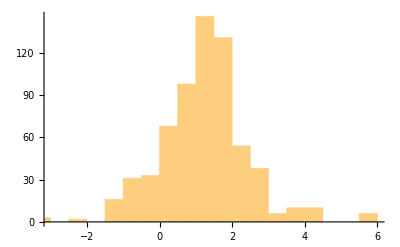

```mathematica
Histogram@af2
```

```mathematica
af[[i]]~Manipulate~{i,1,Length@af,1}
```

```mathematica
Mean[af]//N
```

0.0019084 (4821.43+41+3. √1 Sign[18.9096 (1)-45.9066 1-5.30465 (0.149511 (3.24445+Cot[VectorAngle[{0.117648,-0.0276193,0.982461}+{0.372325,-0.107709,-0.90843,0.260207,-0.233431,-0.901957},{0.073845,0.121891,0.965397}+{0.372325,4,-0.901957}]])+7+0.135329 (1))])
 |  |  |  |